## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 20; mu = 0.1;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.26106+5.26262×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

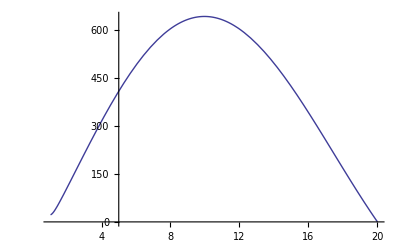

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{5.,5.26263×10^-7},{5.05,5.55934×10^-7},{5.1,5.8674×10^-7},{5.15,6.18704×10^-7},{5.2,6.51851×10^-7},{5.25,6.86213×10^-7},{5.3,7.21794×10^-7},{5.35,7.5864×10^-7},{5.4,7.96769×10^-7},{5.45,8.36211×10^-7},{5.5,8.76985×10^-7},{5.55,9.19118×10^-7},{5.6,9.62645×10^-7},{5.65,1.00758×10^-6},{5.7,1.05396×10^-6},{5.75,1.10178×10^-6},{5.8,1.15116×10^-6},{5.85,1.20202×10^-6},{5.9,1.25445×10^-6},{5.95,1.30845×10^-6},{6.,1.36405×10^-6},{6.05,1.42131×10^-6},{6.1,1.48022×10^-6},{6.15,1.54083×10^-6},{6.2,1.60315×10^-6},{6.25,1.66724×10^-6},{6.3,1.73311×10^-6},{6.35,1.80081×10^-6},{6.4,1.87034×10^-6},{6.45,1.94173×10^-6},{6.5,2.01505×10^-6},{6.55,2.0903×10^-6},{6.6,2.16752×10^-6},{6.65,2.24674×10^-6},{6.7,2.32799×10^-6},{6.75,2.4113×10^-6},{6.8,2.49672×10^-6},{6.85,2.58425×10^-6},{6.9,2.67396×10^-6},{6.95,2.76586×10^-6},{7.,2.85999×10^-6},{7.05,2.9563×10^-6},{7.1,3.05507×10^-6},{7.15,3.15609×10^-6},{7.2,3.25948×10^-6},{7.25,3.36526×10^-6},{7.3,3.47348×10^-6},{7.35,3.58417×10^-6},{7.4,3.69738×10^-6},{7.45,3.81312×10^-6},{7.5,3.93143×10^-6},{7.55,4.05236×10^-6},{7.6,4.17594×10^-6},{7.65,4.30221×10^-6},{7.7,4.43119×10^-6},{7.75,4.56292×10^-6},{7.8,4.69749×10^-6},{7.85,4.83487×10^-6},{7.9,4.97514×10^-6},{7.95,5.11831×10^-6},{8.,5.26441×10^-6},{8.05,5.41353×10^-6},{8.1,5.56566×10^-6},{8.15,5.72086×10^-6},{8.2,5.87917×10^-6},{8.25,6.04061×10^-6},{8.3,6.20525×10^-6},{8.35,6.37308×10^-6},{8.4,6.54422×10^-6},{8.45,6.71865×10^-6},{8.5,6.89632×10^-6},{8.55,7.07756×10^-6},{8.6,7.26215×10^-6},{8.65,7.4502×10^-6},{8.7,7.64165×10^-6},{8.75,7.83686×10^-6},{8.8,8.03555×10^-6},{8.85,8.23788×10^-6},{8.9,8.44389×10^-6},{8.95,8.6536×10^-6},{9.,8.86711×10^-6},{9.05,9.08437×10^-6},{9.1,9.30553×10^-6},{9.15,9.53055×10^-6},{9.2,9.75947×10^-6},{9.25,9.99243×10^-6},{9.3,0.0000102294},{9.35,0.0000104704},{9.4,0.0000107155},{9.45,0.0000109648},{9.5,0.0000112182},{9.55,0.0000114759},{9.6,0.0000117379},{9.65,0.0000120042},{9.7,0.0000122749},{9.75,0.00001255},{9.8,0.0000128295},{9.85,0.0000131136},{9.9,0.0000134022},{9.95,0.0000136954},{10.,0.0000139932},{10.05,0.0000142958},{10.1,0.000014603},{10.15,0.0000149151},{10.2,0.0000152319},{10.25,0.0000155537},{10.3,0.0000158803},{10.35,0.0000162119},{10.4,0.0000165486},{10.45,0.0000168902},{10.5,0.000017237},{10.55,0.0000175889},{10.6,0.000017946},{10.65,0.0000183083},{10.7,0.0000186759},{10.75,0.0000190489},{10.8,0.0000194273},{10.85,0.0000198111},{10.9,0.0000202003},{10.95,0.000020595},{11.,0.0000209953},{11.05,0.0000214013},{11.1,0.0000218128},{11.15,0.0000222301},{11.2,0.0000226532},{11.25,0.000023082},{11.3,0.0000235166},{11.35,0.0000239573},{11.4,0.0000244037},{11.45,0.0000248562},{11.5,0.0000253147},{11.55,0.0000257793},{11.6,0.00002625},{11.65,0.0000267268},{11.7,0.0000272099},{11.75,0.0000276993},{11.8,0.0000281949},{11.85,0.000028697},{11.9,0.0000292054},{11.95,0.0000297202},{12.,0.0000302416},{12.05,0.0000307695},{12.1,0.0000313039},{12.15,0.000031845},{12.2,0.0000323928},{12.25,0.0000329472},{12.3,0.0000335085},{12.35,0.0000340765},{12.4,0.0000346514},{12.45,0.0000352333},{12.5,0.000035822},{12.55,0.0000364177},{12.6,0.0000370205},{12.65,0.0000376304},{12.7,0.0000382474},{12.75,0.0000388715},{12.8,0.0000395028},{12.85,0.0000401415},{12.9,0.0000407874},{12.95,0.0000414406},{13.,0.0000421012},{13.05,0.0000427693},{13.1,0.0000434448},{13.15,0.0000441279},{13.2,0.0000448185},{13.25,0.0000455166},{13.3,0.0000462225},{13.35,0.0000469359},{13.4,0.0000476572},{13.45,0.0000483861},{13.5,0.000049123},{13.55,0.0000498676},{13.6,0.0000506201},{13.65,0.0000513806},{13.7,0.000052149},{13.75,0.0000529254},{13.8,0.0000537099},{13.85,0.0000545025},{13.9,0.0000553031},{13.95,0.000056112},{14.,0.000056929},{14.05,0.0000577543},{14.1,0.0000585879},{14.15,0.0000594297},{14.2,0.00006028},{14.25,0.0000611386},{14.3,0.0000620057},{14.35,0.0000628812},{14.4,0.0000637652},{14.45,0.0000646578},{14.5,0.0000655589},{14.55,0.0000664686},{14.6,0.000067387},{14.65,0.000068314},{14.7,0.0000692498},{14.75,0.0000701943},{14.8,0.0000711476},{14.85,0.0000721098},{14.9,0.0000730806},{14.95,0.0000740605},{15.,0.0000750493}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{5.,5.26263×10^-7},{4.95,4.97701×10^-7},{4.9,4.70229×10^-7},{4.85,4.43813×10^-7},{4.8,4.1844×10^-7},{4.75,3.94074×10^-7},{4.7,3.70711×10^-7},{4.65,3.48303×10^-7},{4.6,3.26849×10^-7},{4.55,3.06317×10^-7},{4.5,2.86685×10^-7},{4.45,2.67935×10^-7},{4.4,2.50045×10^-7},{4.35,2.32981×10^-7},{4.3,2.16735×10^-7},{4.25,2.01281×10^-7},{4.2,1.86597×10^-7},{4.15,1.72665×10^-7},{4.1,1.59458×10^-7},{4.05,1.46962×10^-7},{4.,1.35152×10^-7},{3.95,1.24007×10^-7},{3.9,1.13553×10^-7},{3.85,1.03642×10^-7},{3.8,9.43738×10^-8},{3.75,8.5692×10^-8},{3.7,7.75557×10^-8},{3.65,7.00058×10^-8},{3.6,6.2961×10^-8},{3.55,5.6422×10^-8},{3.5,5.03689×10^-8},{3.45,4.4779×10^-8},{3.4,3.96443×10^-8},{3.35,3.49331×10^-8},{3.3,3.06294×10^-8},{3.25,2.67138×10^-8},{3.2,2.3167×10^-8},{3.15,1.99692×10^-8},{3.1,1.71007×10^-8},{3.05,1.45406×10^-8},{3.,1.22678×10^-8},{2.95,1.02641×10^-8},{2.9,8.5033×10^-9},{2.85,6.97221×10^-9},{2.8,5.64628×10^-9},{2.75,4.4739×10^-9},{2.7,3.45743×10^-9},{2.65,2.55468×10^-9},{2.6,1.72797×10^-9},{2.55,9.3503×10^-10},{2.5,1.25612×10^-10},{2.45,-7.59785×10^-10},{2.4,-1.79216×10^-9},{2.35,-3.10184×10^-9},{2.3,-4.66877×10^-9},{2.25,-6.68984×10^-9},{2.2,-9.19601×10^-9},{2.15,-1.2668×10^-8},{2.1,-1.6935×10^-8},{2.05,-2.23213×10^-8},{2.,-2.90405×10^-8},{1.95,-3.73456×10^-8},{1.9,-4.75132×10^-8},{1.85,-5.98425×10^-8},{1.8,-7.46668×10^-8},{1.75,-9.23466×10^-8},{1.7,-1.13288×10^-7},{1.65,-1.37879×10^-7},{1.6,-1.66679×10^-7},{1.55,-1.99986×10^-7},{1.5,-2.38542×10^-7},{1.45,-2.82813×10^-7},{1.4,-3.33465×10^-7},{1.35,-3.91153×10^-7},{1.3,-4.56581×10^-7},{1.25,-5.30522×10^-7},{1.2,-6.13786×10^-7},{1.15,-7.07259×10^-7},{1.1,-8.11853×10^-7},{1.05,-9.28624×10^-7},{1.,-1.05857×10^-6},{0.95,-1.20284×10^-6},{0.9,-1.3626×10^-6},{0.85,-1.53923×10^-6},{0.8,-1.734×10^-6},{0.75,-1.94843×10^-6},{0.7,-2.18393×10^-6},{0.65,-2.44221×10^-6},{0.6,-2.72509×10^-6},{0.55,-3.03424×10^-6},{0.5,-3.37165×10^-6},{0.45,-3.73935×10^-6},{0.4,-4.13951×10^-6},{0.35,-4.57441×10^-6},{0.3,-5.04645×10^-6},{0.25,-5.55819×10^-6},{0.2,-6.11229×10^-6},{0.15,-6.71159×10^-6},{0.1,-7.35906×10^-6},{0.05,-8.05785×10^-6},{0.,-8.81125×10^-6}}

```mathematica
(*The imaginary part vs the radius*)
```

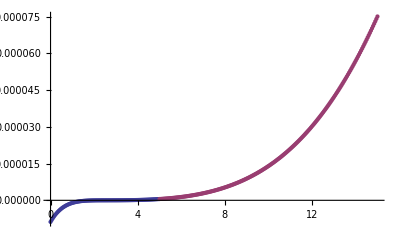

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

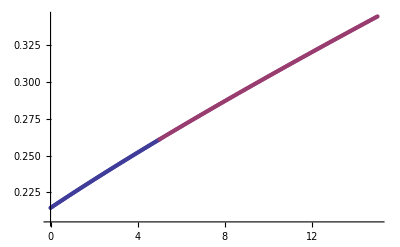

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=20/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=20/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=20/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=20/Q=0.999/I.dat